## Load files with data

```mathematica
elements={"u235","pu239","u238"};
plotNames={"1s","1minute","1hour",(*"24hours",*)"1week","1year","CFY"(*,"CFY_gamma"*)};
forPlot={};
```

```mathematica
For[i=1,i≤Length@elements,i++,
filenames =FileNameJoin[{NotebookDirectory[],elements[[i]]<>"time"<>#<>".dat"}]&/@plotNames;
data=Import[#,"Data"]&/@filenames;
AppendTo[forPlot,elements[[i]]->data]
]
(*maximumData=Import[FileNameJoin[{NotebookDirectory[],"maximum_time.dat"}],"Data"];*)
```

## Neutrino spectrum plots

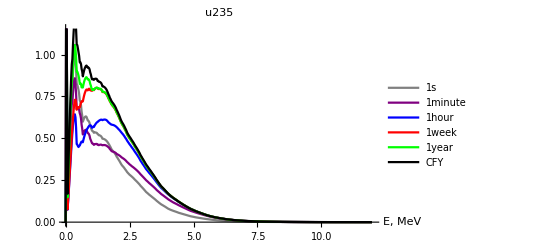

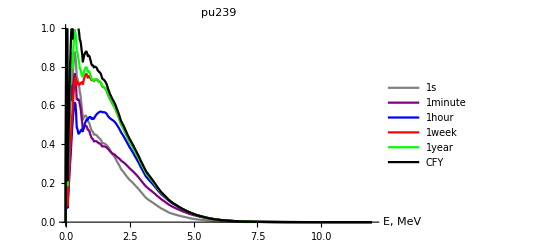

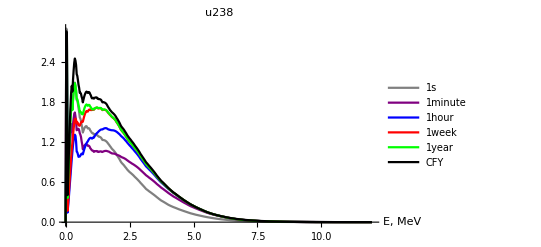

```mathematica
ListPlot[forPlot[[1,2]],PlotStyle->{Gray,Purple,Blue,Red,Green,Black,Pink},AxesLabel->{"E, MeV"},Joined->True,PlotLegends->plotNames,
PlotRange->{{0,12},Automatic},PlotLabel->forPlot[[1,1]]]
ListPlot[forPlot[[2,2]],PlotStyle->{Gray,Purple,Blue,Red,Green,Black,Pink},AxesLabel->{"E, MeV"},Joined->True,PlotLegends->plotNames,
PlotRange->{{0,12},Automatic},PlotLabel->forPlot[[2,1]]]
ListPlot[forPlot[[3,2]],PlotStyle->{Gray,Purple,Blue,Red,Green,Black,Pink},AxesLabel->{"E, MeV"},Joined->True,PlotLegends->plotNames,
PlotRange->{{0,12},Automatic},PlotLabel->forPlot[[3,1]]]
```

```mathematica
CFY baseds plots
```

Part::partw: Part 7 of {{{0.,0.},{0.024,3.29506},{0.048,1.9426},{0.072,0.353455},{0.096,0.572047},{0.12,0.80591},{0.144,1.03082},{0.168,1.205},«35»,{1.032,1.09085},{1.056,1.08542},{1.08,1.08209},{1.104,1.06598},{1.128,1.06972},{1.152,1.07129},{1.176,1.06933},«450»},«4»,{{0.,0.},«49»,«450»}} does not exist.

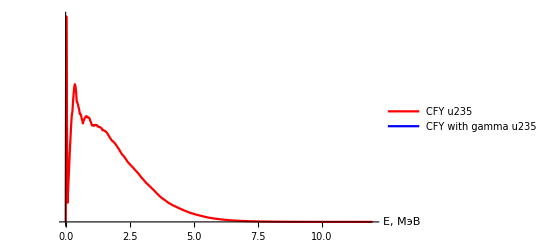

```mathematica
ListPlot[{forPlot[[1,2,6]],forPlot[[1,2,7]]},Joined->True,PlotLegends->{"CFY u235","CFY with gamma u235"},PlotRange->All,AxesLabel->{"E, МэВ"},PlotStyle->{Red,Blue},Ticks->{Automatic,None}]
```

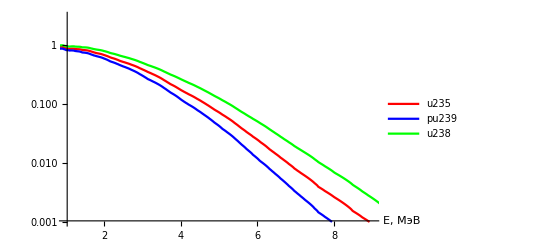

```mathematica
ListLogPlot[{forPlot[[1,2,6]],forPlot[[2,2,6]],forPlot[[3,2,6]]},Joined->True,PlotLegends->elements,AxesLabel->{"E, МэВ"},PlotStyle->{Red,Blue,Green},Ticks->{Automatic,Automatic},PlotRange->{{1,9},{0.001,3}}]
```

```mathematica
posCFYyear=Position[plotNames,"CFY"][[1,1]];
u235year=forPlot[[1,2,posCFYyear]];
pu239year=forPlot[[2,2,posCFYyear]];
ratio=u235year[[All,2]]/pu239year[[All,2]];
ratioPlot={};
For[i=2,i≤Length@ratio,i++,AppendTo[ratioPlot,{u235year[[i,1]],ratio[[i]]}]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

```mathematica
ratioPlot;
```

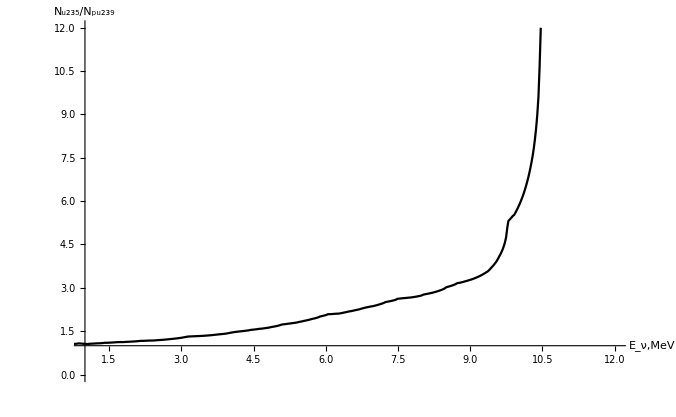

```mathematica
ListPlot[ratioPlot,PlotRange->{{1,12},Automatic},AxesOrigin->{1,1},Joined->True,AxesLabel->{"E_ν,MeV","N_u235/N_pu239"},PlotStyle->Black]
```

## Normalized plots

```mathematica
dataNormalized={};
data=forPlot[[1,2]];
For[i=1,i≤Length@data,i++,
AppendTo[dataNormalized,
{#[[1]],#[[2]]/Max[data[[i]][[All,2]]]}&/@data[[i]]
]
]
```

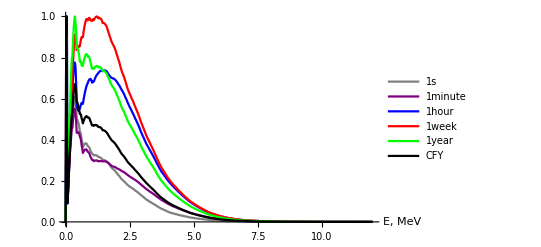

```mathematica
ListPlot[dataNormalized,PlotStyle->{Gray,Purple,Blue,Red,Green,Black},AxesLabel->{"E, MeV"},Joined->True,PlotLegends->plotNames]
```

```mathematica
Plot3D
```

```mathematica
dataCFYNormalized={};5n
data={forPlot[[1,2,6]],forPlot[[2,2,6]]};
For[i=1,i≤Length@data,i++,
AppendTo[dataCFYNormalized,
{#[[1]],#[[2]]/Max[data[[i]][[All,2]]]}&/@data[[i]]
]
]
```

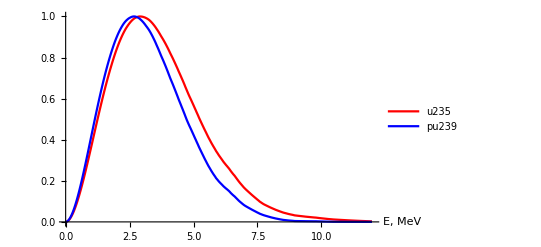

```mathematica
ListPlot[dataCFYNormalized,PlotStyle->{Red,Blue},AxesLabel->{"E, MeV"},Joined->True,PlotLegends->elements,PlotRange->{{0,12},Automatic}]
```

## With gamma

```mathematica
forPlot0={};
For[i=1,i≤Length@elements,i++,
filenames =FileNameJoin[{NotebookDirectory[],elements[[i]]<>"time"<>#<>"_gamma"<>".dat"}]&/@plotNames;
data=Import[#,"Data"]&/@filenames;
AppendTo[forPlot0,elements[[i]]->data]
]
(*maximumData=Import[FileNameJoin[{NotebookDirectory[],"maximum_time.dat"}],"Data"];*)
```

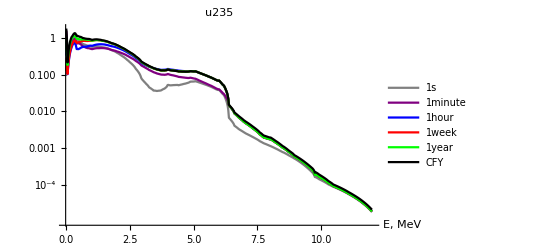

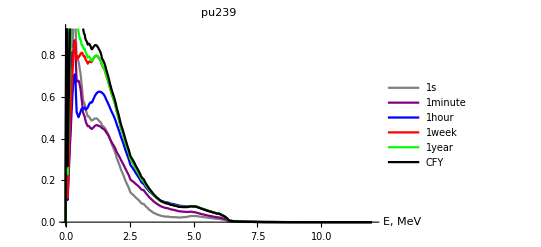

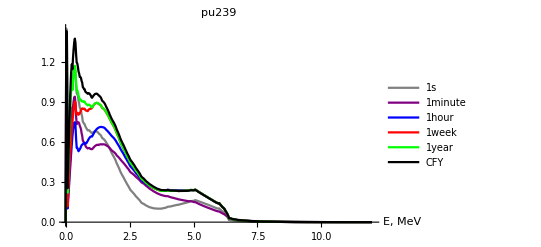

```mathematica
ListLogPlot[forPlot0[[1,2]],PlotStyle->{Gray,Purple,Blue,Red,Green,Black},AxesLabel->{"E, MeV"},Joined->True,PlotLegends->plotNames,
PlotRange->{{0,12},Automatic},PlotLabel->forPlot0[[1,1]]]
ListPlot[forPlot0[[2,2]],PlotStyle->{Gray,Purple,Blue,Red,Green,Black},AxesLabel->{"E, MeV"},Joined->True,PlotLegends->plotNames,
PlotRange->{{0,12},Automatic},PlotLabel->forPlot0[[2,1]]]
ListPlot[forPlot0[[3,2]],PlotStyle->{Gray,Purple,Blue,Red,Green,Black},AxesLabel->{"E, MeV"},Joined->True,PlotLegends->plotNames,
PlotRange->{{0,12},Automatic},PlotLabel->forPlot0[[2,1]]]
```

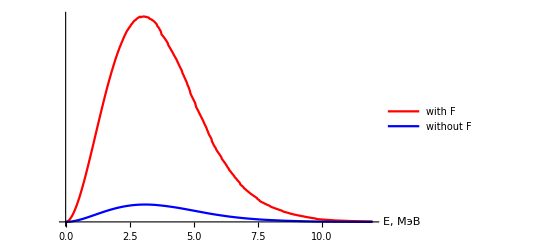

```mathematica
ListPlot[{forPlot[[1,2,6]],forPlot0[[1,2,6]]},Joined->True,PlotLegends->{"with F","without F"},PlotRange->All,AxesLabel->{"E, МэВ"},PlotStyle->{Red,Blue},Ticks->{Automatic,None}]
```